```mathematica
ClearAll["Global`*"]
```

Derive the\chi^2 dependence of energy density by inversion

```mathematica
ϵ[χ2]=(χ2+μ^2)*(3*χ2-μ^2)/(2*λ)
```

((μ^2+χ2) (-μ^2+3 χ2))/(2 λ)

```mathematica
Solve[(χ2+μ^2)*(3*χ2-μ^2)/(2*λ)==ϵ,χ2]
```

{{χ2→1/3 (-μ^2-√2 √(3 ϵ λ+2 μ^4))},{χ2→1/3 (-μ^2+√2 √(3 ϵ λ+2 μ^4))}}

```mathematica
f[p_,η_]=Exp[I*p*Cosh[η]]
g[p_,ϕ_]=Exp[-I*p*Cos[ϕ]]
h1[p_,η_]=Cos[p*Cosh[η]]
h2[p_,η_]=Sin[p*Cosh[η]]
```

ⅇ^(ⅈ p Cosh[η])

ⅇ^(-ⅈ p Cos[ϕ])

Cos[p Cosh[η]]

Sin[p Cosh[η]]

```mathematica
Integrate[g[ϕ],{ϕ,0,2*Pi}]
```

∫_0^(2 π) g[ϕ]ⅆϕ

```mathematica
ps=Range[0.01,50,0.1];
```

```mathematica
h1ps=NIntegrate[h1[ps,η],{η,0,10}];
h2ps=NIntegrate[h2[ps,η],{η,0,10}];
```

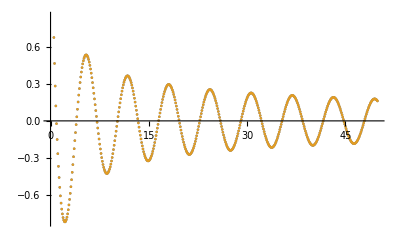

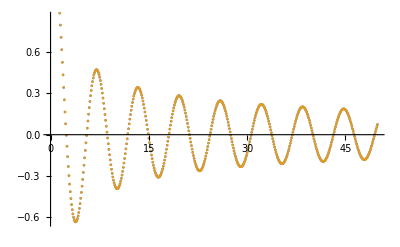

```mathematica
ListPlot[{
Transpose@{ps,h1ps},
Transpose@{ps,-Pi/2*BesselY[0,ps]}
}]
ListPlot[{
Transpose@{ps,h2ps},
Transpose@{ps,Pi/2*BesselJ[0,ps]}
}]
```

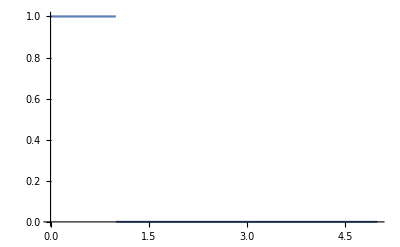

```mathematica
ϕ[r_]=HeavisideTheta[1-r];
Plot[ϕ[r],{r,0,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.317965 and 0.000806564 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.322817 and 0.000817644 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.00494}. NIntegrate obtained -0.331199 and 0.000835509 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

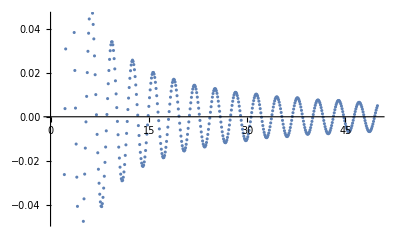

```mathematica
ϕ[r_]=HeavisideTheta[1-r];
ps=Range[0.01,50,0.1];

dr=0.01;
rmin=0.01;
rmax=10;
rs=Range[rmin,rmax,dr];

fNintps=NIntegrate[r*ps*ϕ[r]*BesselJ[0,r*ps]*BesselY[1,ps],{r,rmin,rmax}];
fSum[p_]=dr*Total[rs*p*ϕ[rs]*BesselJ[0,rs*p]*BesselY[1,p]];
fSumps=fSum[ps];

A=ListPlot[{
Transpose@{ps,fNintps},
Transpose@{ps,fSumps}
}]
```

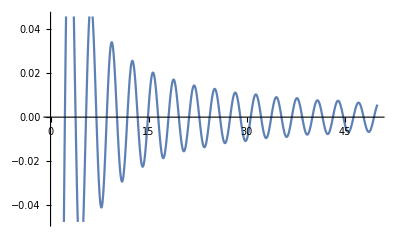

```mathematica
f[p_]=Integrate[r*p*ϕ[r]*BesselJ[0,r*p]*BesselY[1,p],{r,rmin,rmax}];
B=Plot[f[p],{p,0,50}]
```

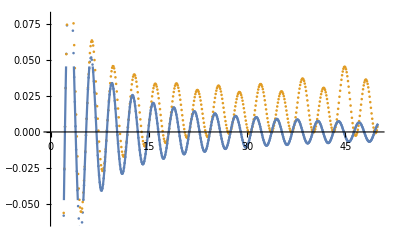

```mathematica
Show[A,B]
```

```mathematica
a={1,2,3,4,5}
b=a^2
```

{1,2,3,4,5}

{1,4,9,16,25}

```mathematica
Transpose[{a,b}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25}}

```mathematica
test=Interpolation[Transpose[{a,b}]]
```

InterpolatingFunction[…]

```mathematica
test[2.5]
```

6.25

```mathematica
x[r_,ϕ_]=r*Cos[ϕ];
y[r_,ϕ_]=r*Sin[ϕ];
z[τ_,η_]=τ*Cosh[η];
t[τ_,η_]=τ*Sinh[η];

r[x_,y_]=Sqrt[x^2+y^2];
τ[t_,z_]=Sqrt[t^2-z^2];
ϕ[x_,y_]=ArcTan[y/x];
η[z_,t_]=ArcTanh[z/t];
```

```mathematica
F=f[τ[t,z],r[x,y]];
(-D[F,{t,2}]+D[F,{x,2}]+D[F,{y,2}]+D[F,{z,2}])/.x->x[r,ϕ]/.y->y[r,ϕ]/.z->z[τ,η]/.t->t[τ,η]//FullSimplify
```

(f^(0,1)[√(-τ^2),√(r^2)])/(√(r^2))+f^(0,2)[√(-τ^2),√(r^2)]-(f^(1,0)[√(-τ^2),√(r^2)])/(√(-τ^2))-f^(2,0)[√(-τ^2),√(r^2)]

```mathematica
ClearAll["Global`*"]
DSolve[-(1/τ)*D[τ*D[y[τ,r],{τ,1}],{τ,1}]==A*y[τ,r],y[τ,r],τ]
```

{{y[τ,r]→BesselJ[0,√A τ] C[1]+BesselY[0,√A τ] C[2]}}

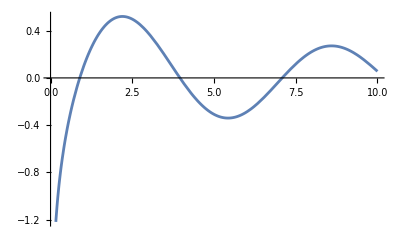

```mathematica
Plot[BesselY[0,x],{x,0,10}]
```

```mathematica
BesselY[0,I]//N
```

-0.268032+1.26607 ⅈ

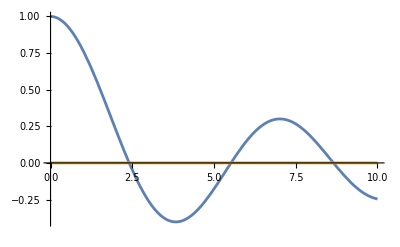

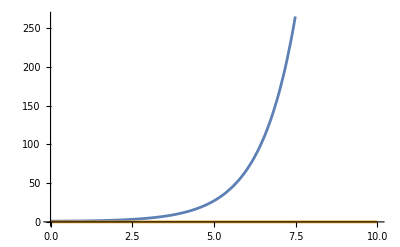

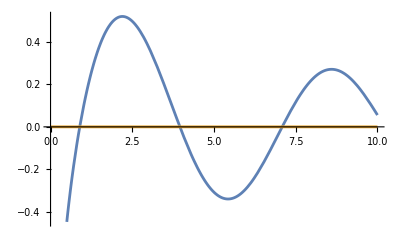

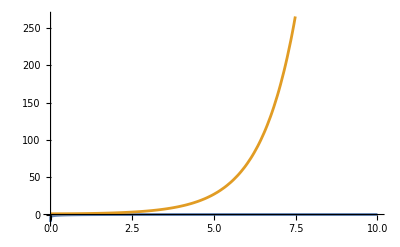

```mathematica
Plot[{Re@BesselJ[0,x],Im@BesselJ[0,x]},{x,0,10}]
Plot[{Re@BesselJ[0,I*x],Im@BesselJ[0,I*x]},{x,0,10}]
Plot[{Re@BesselY[0,x],Im@BesselY[0,x]},{x,0,10}]
Plot[{Re@BesselY[0,I*x],Im@BesselY[0,I*x]},{x,0,10}]
```

```mathematica
Integrate[1/Sqrt[m^2-x^2-y^2],{y,-Sqrt[m^2-x^2],Sqrt[m^2-x^2]}]
```

ConditionalExpression[π, x^2<m^2]

```mathematica
Integrate[Sin[x],{x,0,Pi}]
```

2

```mathematica
Integrate[2*Sqrt[m^2-x^2],{x,-m,m}]
```

m √(m^2) π

```mathematica
ma=0.6;
mb=0.14;
mc=0.14;
pabc=Sqrt[((ma+mb)^2-mc^2)*((ma-mb)^2-mc^2)]/(2*ma);
Eabc=Sqrt[mb^2+pabc^2];
Q=1;
w[p_,m_]=Sqrt[p^2+m^2];
ustar[t_,ϕ_,p_]=(ma*Eabc+t*Q*p*Cos[ϕ])/(w[t*Q,ma]*w[p,mb]);
ηstar[t_,ϕ_,p_]=ArcCosh[ustar[t,ϕ,p]];
absgradg[t_,η_,ϕ_,p_]=Sqrt[(-w[p,mb]/w[q,ma]*Q^2*t*Cosh[η]+Q*p*Cos[ϕ])^2+(w[Q*t,ma]*w[p,mb]*Sinh[η])^2+(t*Q*p*Sin[ϕ])^2];
areafactor[t_,ϕ_,p_]=Sqrt[1/(ustar[t,ϕ,p]^2-1)*((Q*p)/(w[Q*t,ma]*w[p,mb]))^2*((Cos[ϕ]*(1-((t*Q)/w[t*Q,ma])^2))^2+(t*Sin[ϕ])^2)+1]
```

√(1+(p^2 ((1-t^2/(0.36+t^2))^2 Cos[ϕ]^2+t^2 Sin[ϕ]^2))/((0.0196+p^2) (0.36+t^2) (-1+(0.18+p t Cos[ϕ])^2/((0.0196+p^2) (0.36+t^2)))))

```mathematica
Manipulate[
Plot3D[areafactor[t,ϕ,P],{t,0,10},{ϕ,0,π}],
{P,0,3}]
```

```mathematica
Manipulate[
ContourPlot[{ustar[t,ϕ,P]==1},{t,0,10},{ϕ,0,π}],
{P,0,3}]
```

```mathematica
ClearAll["Global`*"]
ma=0.6;
mb=0.14;
mc=0.14;
pabc=Sqrt[((ma+mb)^2-mc^2)*((ma-mb)^2-mc^2)]/(2*ma);
Eabc=Sqrt[mb^2+pabc^2];
w[px_,py_,pz_,m_]=Sqrt[px^2+py^2+pz^2+m^2];
s=Solve[-w[px,py,pz,mb]*w[qx,qy,qz,ma]+pz*qz+px*qx+py*qy+ma*Eabc==0,qz]//FullSimplify;
QZ[qx_,qy_,px_,py_,pz_]=qz/.s[[1]]//FullSimplify;
Sigma[qx_,qy_,px_,py_,pz_]:=Sqrt[1+(D[QZ[t,qy,px,py,pz],t]/.t->qx)^2+(D[QZ[qx,t,px,py,pz],t]/.t->qy)^2];
absgradg[qx_,qy_,qz_,px_,py_,pz_]=Sqrt[(w[px,py,pz,mb]/w[qx,qy,qz,ma])^2*(qx^2+qy^2+qz^2)-2(w[px,py,pz,mb]/w[qx,qy,qz,ma])*(qx*px+qy*py+qz*pz)+(px^2+py^2+pz^2)];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

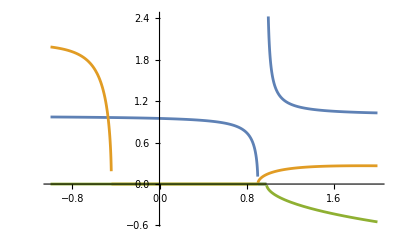

```mathematica
Plot[{
Re@Sigma[qx,0,1,0,0],
Re@absgradg[qx,0,QZ[qx,0,1,0,0],1,0,0],
Re@QZ[qx,0,1,0,0]
},{qx,-1,2}]
```

```mathematica
ClearAll["Global`*"]
ma=0.6;
mb=0.14;
mc=0.14;
pabc=Sqrt[((ma+mb)^2-mc^2)*((ma-mb)^2-mc^2)]/(2*ma);
Eabc=Sqrt[mb^2+pabc^2];
s=Solve[-((pz*qz+pT*qT*Cos[ϕ]+ma*Eabc)/p0)^2+qz^2+qT^2+ma^2==0,qz]/.p0->Sqrt[mb^2+pz^2+pT^2]//FullSimplify
QZ[qT_,ϕ_,pz_,pT_]=qz/.s[[1]]//FullSimplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{qz→(0.18 pz+1. pT pz qT Cos[ϕ]+0.02 √(0.0196+pT^2+pz^2) √(63.36-49. qT^2+pT^2 (-900.-1250. qT^2)+pT qT (900. Cos[ϕ]+1250. pT qT Cos[2. ϕ])))/(0.0196+1. pT^2)},{qz→(0.18 pz+1. pT pz qT Cos[ϕ]-0.02 √(0.0196+pT^2+pz^2) √(63.36-49. qT^2+pT^2 (-900.-1250. qT^2)+pT qT (900. Cos[ϕ]+1250. pT qT Cos[2. ϕ])))/(0.0196+1. pT^2)}}

(0.18 pz+1. pT pz qT Cos[ϕ]+0.02 √(0.0196+pT^2+pz^2) √(63.36-49. qT^2+pT^2 (-900.-1250. qT^2)+pT qT (900. Cos[ϕ]+1250. pT qT Cos[2. ϕ])))/(0.0196+1. pT^2)

```mathematica
f[x_,y_]=(1+x*y)/(√(2+x^2));
NIntegrate[NIntegrate[1/(√(1-y^2)√(f[t,y]^2-1))/.t->x,{y,(√(2+t^2)-1)/t,1}/.t->x]//Evaluate,{x,0.5,1}]
```

NIntegrate::nlim: y = (-1.+√(2.+x^2))/x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

1.17797

```mathematica
Integrate[1/(√(2+x^2))-1/(2 x √(2+x^2)),{x,1/2,10}]
```

(-ArcTanh[3/(2 √2)]+ArcTanh[√51])/(2 √2)-Log[-10+√102]

```mathematica
%//N
```

1.73416+0. ⅈ

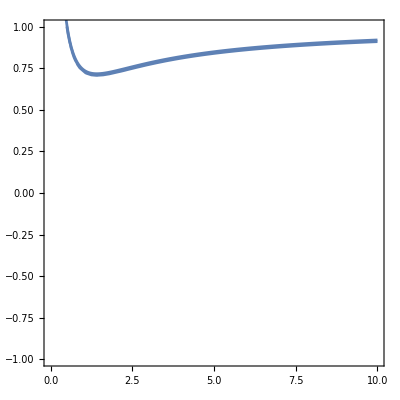

```mathematica
Show[
ContourPlot[f[x,y]==1,{x,0,10},{y,-1,1}],
Plot[(√(2+x^2)-1)/x+0.01,{x,0,10}]
]
```

```mathematica
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Cuhre-Linux"]
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Vegas-Linux"]
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Suave-Linux"]
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Divonne-Linux"]
```

LinkObject[…]

LinkObject[…]

LinkObject[…]

«1 more identical outputs»

```mathematica
f[x_,y_]=(1+x*y)/(√(2+x^2));
Cuhre[1/(√(1-y^2)√(f[x,y]^2-1)),{x,0.5,10},{y,(√(2+x^2)-1)/x,1},Verbose->0]
```

Cuhre::success: Needed 9035 function evaluations on 70 subregions.

{{15.96,0.0151969,4.4213×10^-18}}

```mathematica
Suave[1/(√(1-y^2)√(f[x,y]^2-1)),{x,0.5,10},{y,(√(2+x^2)-1)/x,1},Verbose->0]
```

Suave::accuracy: Desired accuracy was not reached within 50000 function evaluations on 50 subregions.

{{15.9259,0.0161759,1.}}

```mathematica
Vegas[1/(√(1-y^2)√(f[x,y]^2-1)),{x,0.5,10},{y,(√(2+x^2)-1)/x,1},Verbose->0]
```

Vegas::success: Needed 32500 function evaluations.

{{15.9493,0.0153094,0.0119089}}

```mathematica
ClearAll["Global`*"]
ma=0.6;
mb=0.14;
mc=0.14;
pabc=Sqrt[((ma+mb)^2-mc^2)*((ma-mb)^2-mc^2)]/(2*ma);
Eabc=Sqrt[mb^2+pabc^2];
w[p_,m_]=Sqrt[p*p+m*m];
Q=1;
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Cuhre-Linux"];
Install["/media/tobias/data/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/Mathematica/Vegas-Linux"];
absgradg[t_,u_,v_,p_]=√((-t*u*w[p,mb]/w[t*Q,ma]*Q^2+Q*p*v)^2+(w[t*Q,ma]*w[p,mb])^2+(t*Q*p)^2);
areafactor[t_,v_,p_]=√((v*(p*Q)/(w[p,mb]*w[t*Q,ma])*(1-(t^2*Q^2)/w[t*Q,ma]^2))^2+(1)^2+((t*Q*p)/(w[t*Q,ma]*w[p,mb]))^2);
ustar[t_,v_,p_]=(ma*Eabc+Q*p*t*v)/(w[t*Q,ma]*w[p,mb])
```

(0.18+p t v)/(√(0.0196+p^2) √(0.36+t^2))

```mathematica
p=1;
Integrand[t_,v_,p_]=If[ustar[t,v,p]>1,1/(√(ustar[t,v,p]^2-1))*1/(√(1-v^2))*areafactor[t,v,p]/absgradg[t,ustar[t,v,p],v,p],0];
Cuhre[Integrand[t,v,p],{t,0,1},{v,-1,1},Verbose->0,MaxPoints->100000]
```

Cuhre::accuracy: Desired accuracy was not reached within 100035 function evaluations on 770 subregions.

{{0.0260554,0.00465833,3.75015×10^-17}}

```mathematica
s=Solve[1==(A+B*t*v)/(w[t*C,D]*w[F,G]),v]
```

{{v→-(√(F^2+G^2) √(D^2+C^2 t^2) (-1+A/(√(F^2+G^2) √(D^2+C^2 t^2))))/(B t)}}

```mathematica
vmin[t_]=v/.s[[1]]
```

-(√(F^2+G^2) √(D^2+C^2 t^2) (-1+A/(√(F^2+G^2) √(D^2+C^2 t^2))))/(B t)

```mathematica
tmin=t/.Solve[0==D[vmin[t],t],t][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(√(-A^2 D^2+D^4 F^2+D^4 G^2))/(A C)

```mathematica
vmin[tmin]//FullSimplify
```

(A C (-A+√(F^2+G^2) √((D^4 (F^2+G^2))/A^2)))/(B √(-A^2 D^2+D^4 (F^2+G^2)))